```mathematica
f[v_] := (v * (v + 1)) / 127
```

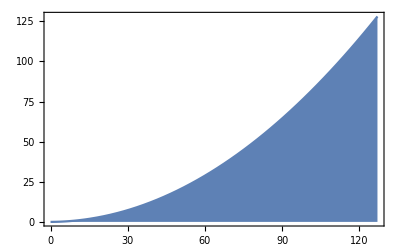

```mathematica
a = Plot[f[v], {v, 0, 127}, Frame->True, Filling->Bottom, FillingStyle->Opactity[1.0],  BaseStyle->{FontSize->14}, FrameStyle->Directive[Thickness[0.002]]]
```

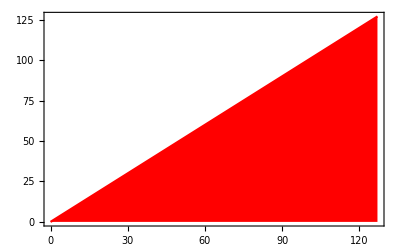

```mathematica
b = Plot[v, {v, 0, 127}, Frame->True, PlotStyle->Red, Filling->Bottom, FillingStyle->Opacity[1.0], BaseStyle->{FontSize->14}, FrameStyle->Directive[Thickness[0.002]]]
```

```mathematica
Export["/tmp/Fade.pdf",  Show[b, a, AspectRatio->1, FrameLabel->{Input Velocity, Output Velocity}]]
```